```mathematica
L=20;p=35*Pi/180;
```

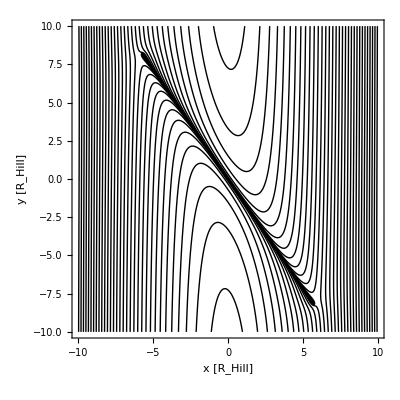

```mathematica
ContourPlot[-3/2*(x^2)-(3/1)Log[(L/2-x Sin[p]+y Cos[p]+Sqrt[(L/2-x Sin[p]+y Cos[p])^2+(x Cos[p]+y Sin[p])^2])/(-(L/2+x Sin[p]-y Cos[p])+Sqrt[(L/2+x Sin[p]-y Cos[p])^2+(x Cos[p]+y Sin[p])^2])+9/2],{x,-(L/2),L/2},{y,-10,10},PlotPoints->100,Contours->32,ColorFunction->GrayLevel,AspectRatio->Automatic,AxesLabel->{Style[xs,Large,Bold,Black],Style[helo,Large,Bold,Black]}, ContourShading->None,LabelStyle->Directive[Large,Black,Bold],FrameLabel->{StringForm["x [R_Hill]"],StringForm["y [R_Hill]"]}]
```